```mathematica
(*    aus Aerosol 0108.nb    *)

char=M = {"C2"->{"age"->28.,"sex"->"m","height"->174.,"weight"->75.,"beard"->"full","resp_dis"->"","nic_abu"->"abu","exper"->20.},"S1"->{"age"->26.,"sex"->"f","height"->172.,"weight"->56.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S2"->{"age"->27.,"sex"->"m","height"->181.,"weight"->64.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""},"S3"->{"age"->20.,"sex"->"d","height"->170.,"weight"->75.,"beard"->"","resp_dis"->"Asthma bronchiale (aktuell nicht exazerbiert)","nic_abu"->"","exper"->""},"S4"->{"age"->30.,"sex"->"f","height"->173.,"weight"->59.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S5"->{"age"->30.,"sex"->"m","height"->180.,"weight"->75.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S6"->{"age"->29.,"sex"->"f","height"->165.,"weight"->58.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S7"->{"age"->27.,"sex"->"f","height"->163.,"weight"->51.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S8"->{"age"->28.,"sex"->"f","height"->162.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->""},"S9"->{"age"->30.,"sex"->"m","height"->169.,"weight"->68.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""},"S10"->{"age"->52.,"sex"->"m","height"->183.,"weight"->80.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->""},"S11"->{"age"->66.,"sex"->"m","height"->183.,"weight"->70.,"beard"->"full","resp_dis"->"allergisches Asthma (saisonal)","nic_abu"->"","exper"->""},"S12"->{"age"->26.,"sex"->"m","height"->173.,"weight"->84.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->""},"O2"->{"age"->63.,"sex"->"f","height"->156.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"O3"->{"age"->56.,"sex"->"f","height"->170.,"weight"->76.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->44.},"O4"->{"age"->53.,"sex"->"f","height"->183.,"weight"->72.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"O5"->{"age"->54.,"sex"->"f","height"->171.,"weight"->70.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->43.},"O6"->{"age"->45.,"sex"->"m","height"->185.,"weight"->90.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->34.},"O7"->{"age"->64.,"sex"->"m","height"->187.,"weight"->82.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"O8"->{"age"->53.,"sex"->"m","height"->203.,"weight"->92.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->40.},"O9"->{"age"->24.,"sex"->"f","height"->160.,"weight"->58.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->14.},"O10"->{"age"->45.,"sex"->"m","height"->186.,"weight"->85.,"beard"->"3d","resp_dis"->"","nic_abu"->"abu","exper"->30.},"O11"->{"age"->65.,"sex"->"m","height"->176.,"weight"->63.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->55.},"O12"->{"age"->42.,"sex"->"m","height"->189.,"weight"->90.,"beard"->"","resp_dis"->"","nic_abu"->"abu","exper"->30.},"F1"->{"age"->63.,"sex"->"m","height"->186.,"weight"->88.,"beard"->"","resp_dis"->"","nic_abu"->"abu","exper"->50.},"F2"->{"age"->47.,"sex"->"f","height"->161.,"weight"->74.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->35.},"F3"->{"age"->47.,"sex"->"f","height"->158.,"weight"->72.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->38.},"F4"->{"age"->68.,"sex"->"f","height"->158.,"weight"->95.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->58.},"F5"->{"age"->63.,"sex"->"f","height"->172.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->53.},"F6"->{"age"->26.,"sex"->"f","height"->166.,"weight"->75.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->15.},"F7"->{"age"->50.,"sex"->"f","height"->156.,"weight"->54.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->39.},"F9"->{"age"->64.,"sex"->"f","height"->164.,"weight"->65.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"F10"->{"age"->26.,"sex"->"f","height"->168.,"weight"->65.,"beard"->"","resp_dis"->"","nic_abu"->"s.p.","exper"->20.},"F11"->{"age"->29.,"sex"->"f","height"->165.,"weight"->57.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->16.},"F12"->{"age"->33.,"sex"->"f","height"->178.,"weight"->80.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->28.},"F13"->{"age"->52.,"sex"->"f","height"->167.,"weight"->60.,"beard"->"","resp_dis"->"allergisches Asthma","nic_abu"->"","exper"->40.},"F14"->{"age"->38.,"sex"->"f","height"->165.,"weight"->66.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->27.},"F15"->{"age"->59.,"sex"->"f","height"->163.,"weight"->55.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->40.},"F16"->{"age"->37.,"sex"->"m","height"->180.,"weight"->76.,"beard"->"3d","resp_dis"->"","nic_abu"->"","exper"->27.},"F17"->{"age"->23.,"sex"->"f","height"->173.,"weight"->56.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->11.},"F18"->{"age"->56.,"sex"->"m","height"->180.,"weight"->80.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->45.},"F19"->{"age"->64.,"sex"->"f","height"->167.,"weight"->50.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->50.},"F20"->{"age"->46.,"sex"->"f","height"->168.,"weight"->61.,"beard"->"","resp_dis"->"","nic_abu"->"","exper"->35.},"T1"->{"age"->26.,"sex"->"m","height"->182.,"weight"->90.,"beard"->"full","resp_dis"->"","nic_abu"->"","exper"->""}};
```

```mathematica
Clear[ToEnglish,Z,newID]

{ToEnglish,Z} = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"];
newID=Map[#[[1]]->StringJoin["P",ToString@#[[2]]]&,Transpose@{Union[Drop[Z[[All,1]],2]],Table[n,{n,Length@Union[Drop[Z[[All,1]],2]]}]}];
```

```mathematica
Union@char[[All,2,All,1]]
```

{{age,sex,height,weight,beard,resp_dis,nic_abu,exper}}

```mathematica
char[[All,2,All,1]][[1]]
```

{age,sex,height,weight,beard,resp_dis,nic_abu,exper}

```mathematica
char=M/. newID;
chars=Association[MapThread[#1->#2&,{vars=char[[All,2,All,1]][[1]],Transpose[char[[All,2,All,2]]]}]]
```

<|age→{28.,26.,27.,20.,30.,30.,29.,27.,28.,30.,52.,66.,26.,63.,56.,53.,54.,45.,64.,53.,24.,45.,65.,42.,63.,47.,47.,68.,63.,26.,50.,64.,26.,29.,33.,52.,38.,59.,37.,23.,56.,64.,46.,26.},sex→{m,f,m,d,f,m,f,f,f,m,m,m,m,f,f,f,f,m,m,m,f,m,m,m,m,f,f,f,f,f,f,f,f,f,f,f,f,f,m,f,m,f,f,m},height→{174.,172.,181.,170.,173.,180.,165.,163.,162.,169.,183.,183.,173.,156.,170.,183.,171.,185.,187.,203.,160.,186.,176.,189.,186.,161.,158.,158.,172.,166.,156.,164.,168.,165.,178.,167.,165.,163.,180.,173.,180.,167.,168.,182.},weight→{75.,56.,64.,75.,59.,75.,58.,51.,55.,68.,80.,70.,84.,55.,76.,72.,70.,90.,82.,92.,58.,85.,63.,90.,88.,74.,72.,95.,55.,75.,54.,65.,65.,57.,80.,60.,66.,55.,76.,56.,80.,50.,61.,90.},beard→{full,,full,,,,,,,full,3d,full,3d,,,,,3d,,3d,,3d,,,,,,,,,,,,,,,,,3d,,,,,full},resp_dis→{,,,Asthma bronchiale (aktuell nicht exazerbiert),,,,,,,,allergisches Asthma (saisonal),,,,,,,,,,,,,,,,,,,,,,,,allergisches Asthma,,,,,,,,},nic_abu→{abu,,,,,,,,,,,,,,s.p.,,s.p.,,,,,abu,,abu,abu,,,,,,,,s.p.,,,,,,,,,,,},exper→{20.,,,,,,,,,,,,,50.,44.,40.,43.,34.,40.,40.,14.,30.,55.,30.,50.,35.,38.,58.,53.,15.,39.,50.,20.,16.,28.,40.,27.,40.,27.,11.,45.,50.,35.,}|>

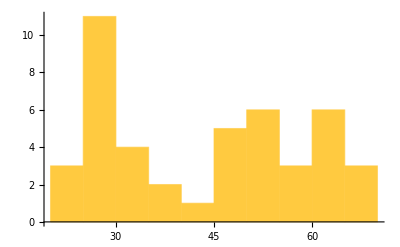

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

{Null,MixtureDistribution[{0.412058,0.382539,0.205403},{NormalDistribution[26.6784,3.41283],NormalDistribution[49.4809,6.66639],NormalDistribution[64.812,1.64939]}],0.000260653,{28.,45.,56.},{20.,68.}}

```mathematica
ageDesc={Histogram[#,{5}],FindDistribution[chars["age"]],KolmogorovSmirnovTest[#],iqrAge=Quartiles[#],minmaxAge=MinMax[#]}&@chars["age"]
```

```mathematica
sexDis=Tally[chars["sex"]]
```

{{m,17},{f,26},{d,1}}

```mathematica
sexDis={#[[1]],Row[{#[[2]]," (",#[[3]],")"}]}&/@Map[Flatten,{sexDis,Round[#,.01]&/@(sexDis[[All,2]]/Total[sexDis[[All,2]]] 1.)}ᵀ  /. {"m"->"male","f"->"female", "d"->"divers"},{1}]
```

{{male,17 (0.39)},{female,26 (0.59)},{divers,1 (0.02)}}

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

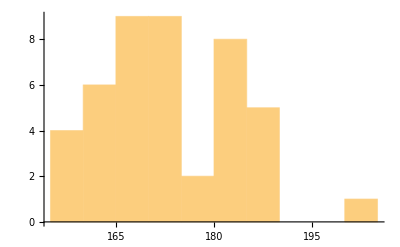
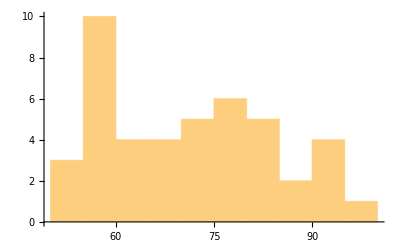
{{-Graphics-,MixtureDistribution[{0.412058,0.382539,0.205403},{NormalDistribution[26.6784,3.41283],NormalDistribution[49.4809,6.66639],NormalDistribution[64.812,1.64939]}],0.403375,{165.,171.5,180.5},{156.,203.}},{-Graphics-,MixtureDistribution[{0.412058,0.382539,0.205403},{NormalDistribution[26.6784,3.41283],NormalDistribution[49.4809,6.66639],NormalDistribution[64.812,1.64939]}],0.267819,{58.,70.,80.},{50.,95.}}}

```mathematica
{ heightDesc, weightDesc}={Histogram[#,{5}],FindDistribution[chars["age"]],KolmogorovSmirnovTest[#],Quartiles[#],MinMax[#]}&/@{chars["height"],chars["weight"]}
```

{25,19,20,26,20,23,21,19,21,24,24,21,28,23,26,21,24,26,23,22,23,25,20,25,25,29,29,38,19,27,22,24,23,21,25,22,24,21,23,19,25,18,22,27}

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

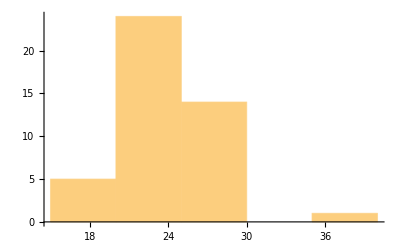
{-Graphics-,MixtureDistribution[{0.412058,0.382539,0.205403},{NormalDistribution[26.6784,3.41283],NormalDistribution[49.4809,6.66639],NormalDistribution[64.812,1.64939]}],0.079733,{21,23,25},{18,38}}

```mathematica
bmi=MapThread[Round[#2/((#1 / 100)^2)]&,{chars["height"],chars["weight"]}]

bmiDesc={Histogram[#,{5}],FindDistribution[chars["age"]],KolmogorovSmirnovTest[#],Quartiles[#],MinMax[#]}&@bmi
```

```mathematica
nicAbuDis=Tally[chars["nic_abu"]]
```

{{abu,4},{,37},{s.p.,3}}

{{{male,17 (0.39)},{female,26 (0.59)},{divers,1 (0.02)}},{{abu,4},{,37},{s.p.,3}}}

```mathematica
tableCharResults=Prepend[{{"age","weight","height","bmi"},Map[Row[{Round@#[[1,2]]," (",
Round@#[[1,1]],"-",Round@#[[1,-1]],", ",Round@#[[2,1]],"-",Round@#[[2,2]],")"}]&,{ageDesc,weightDesc,heightDesc,bmiDesc}[[All,{-2,-1}]]]}ᵀ,{"","median (IQR, Range) or n (%)"}]
```

{{,median (IQR, Range) or n (%)},{age,45 (28-56, 20-68)},{weight,70 (58-80, 50-95)},{height,172 (165-180, 156-203)},{bmi,23 (21-25, 18-38)}}

```mathematica
TableForm@Append[tableCharResults,{sexDis,nicAbuDis}]
```

| median (IQR, Range) or n (%)
age | 45 (28-56, 20-68)
weight | 70 (58-80, 50-95)
height | 172 (165-180, 156-203)
bmi | 23 (21-25, 18-38)
male | 17 (0.39)
female | 26 (0.59)
divers | 1 (0.02) | abu | 4
 | 37
s.p. | 3